```mathematica
ProporcionallyModularAffineSemigroupN2[F1_:Integer,F2_:Integer,b_:Integer,g1_:Integer,g2_:Integer,tope1_:Integer,tope2_:Integer]:=Module[{i,j,f1,f2,S,S1,GS,f,g,d},
If[g1≤0 && g2≤0,Print["Semigrupo= <{0,0}>"];Return[{{0,0}}]];
f1=Mod[F1,b];
f2=Mod[F2,b];
f[{x1_,x2_}]:=f1*x1+f2*x2;
g[{x1_,x2_}]:=g1*x1+g2*x2;
S1=Flatten[Table[{i,j},{i,0,tope1},{j,0,tope2}],1];
S=Select[S1,Mod[f[#],b]≤g[#]&];(*Points of S*)
GS=Complement[S1,S]; (*Gaps of S*)
d[{x1_,x2_}]:=(f1-g1)*x1+(f2-g2)*x2;
Print[
Show[{
ContourPlot[g[{x1,x2}]==0,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Black,Dashed,Thickness[0.009]}],
ContourPlot[g[{x1,x2}]==b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Black,Dashed,Thickness[0.009]}],
ContourPlot[f[{x1,x2}]==0,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Green,Dashed,Thickness[0.009]}],
ContourPlot[f[{x1,x2}]==b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Green,Dashed,Thickness[0.009]}],
ContourPlot[f[{x1,x2}]==2*b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Green,Dashed,Thickness[0.009]}],
ContourPlot[f[{x1,x2}]==3*b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Green,Dashed,Thickness[0.009]}],
ContourPlot[f[{x1,x2}]==4*b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Green,Dashed,Thickness[0.009]}],
ContourPlot[d[{x1,x2}]==0,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Blue,Dashed,Thickness[0.009]}],
ContourPlot[d[{x1,x2}]==b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Blue,Dashed,Thickness[0.009]}],
ContourPlot[d[{x1,x2}]==2*b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Blue,Dashed,Thickness[0.009]}],
ContourPlot[d[{x1,x2}]==3*b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Blue,Dashed,Thickness[0.009]}],
ContourPlot[d[{x1,x2}]==4*b,{x1,-10,tope1},{x2,-10,tope2},ContourStyle->{Blue,Dashed,Thickness[0.009]}],
ListPlot[S,PlotStyle->{PointSize[0.012],Directive[Red]}],
ListPlot[GS,PlotStyle->{PointSize[0.012],Directive[Black]}]
},AspectRatio->Automatic,Axes->True,PlotRange->{{-2,tope1},{-2,tope2}}
]
];
Return[];
];
```

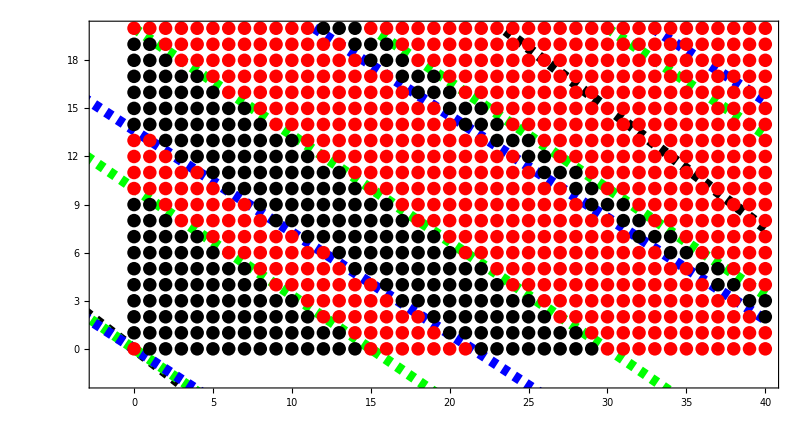

```mathematica
ProporcionallyModularAffineSemigroupN2[10,15,150,3,4,40,20]
```

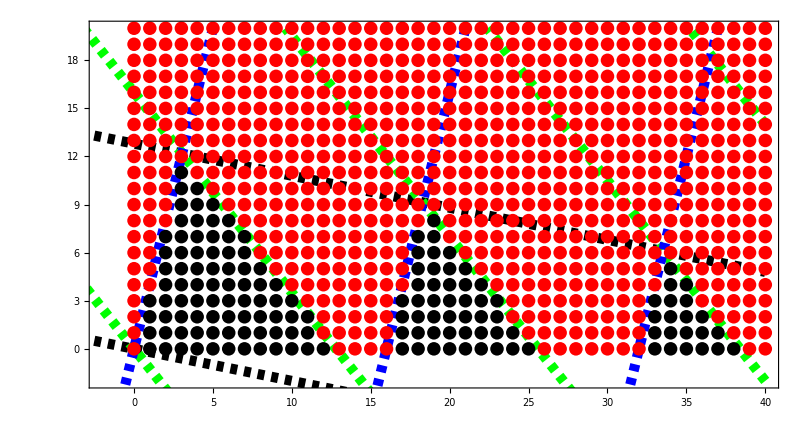

```mathematica
ProporcionallyModularAffineSemigroupN2[5,4,64,1,5,40,20]
```

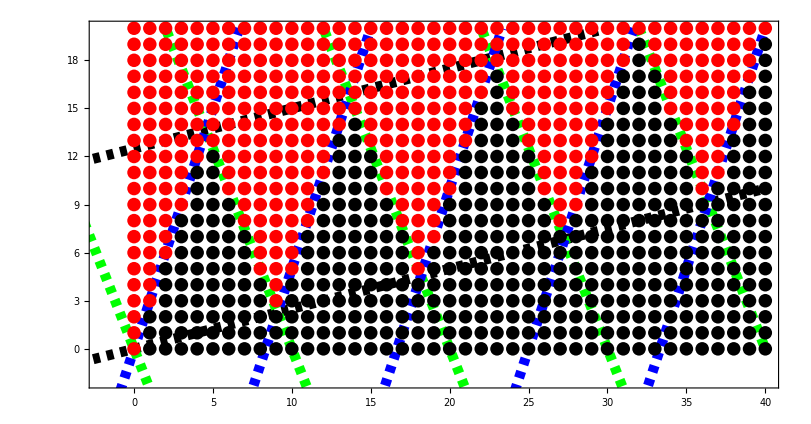

```mathematica
ProporcionallyModularAffineSemigroupN2[5,2,50,-1,4,40,20]
```

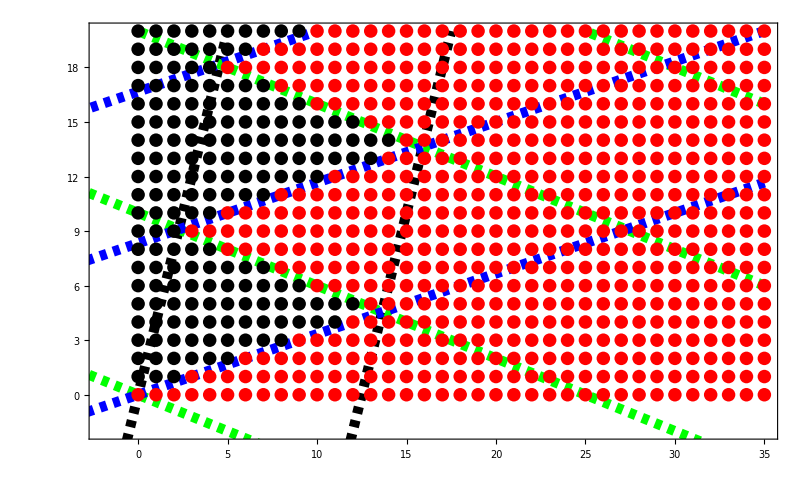

```mathematica
ProporcionallyModularAffineSemigroupN2[2,5,50,4,-1,35,20]
```

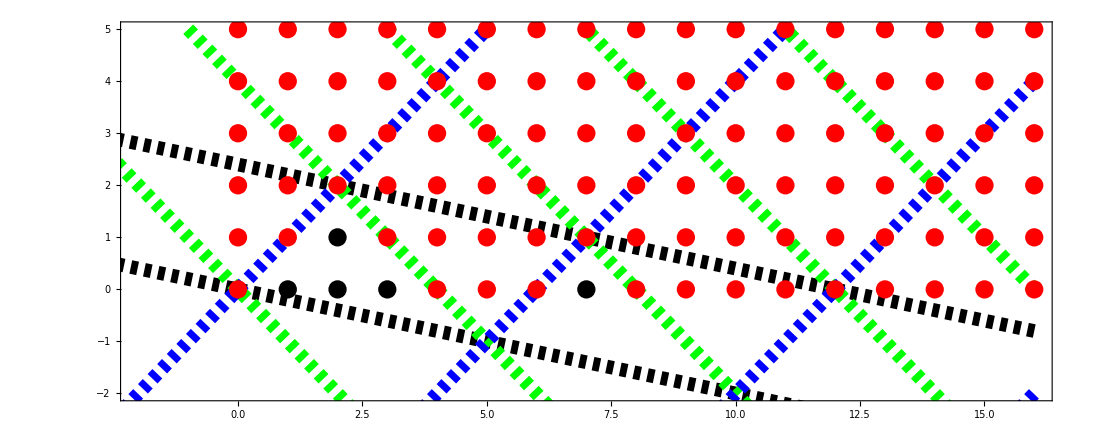

```mathematica
ProporcionallyModularAffineSemigroupN2[12,12,48,4,20,16,5]
```